```mathematica
LineWebPainting[img_,k_:100]:=Module[{radon,lhalf,inverseDualRadon,lines},
If[k===0,Return[img]];
radon=Radon[ColorNegate@ColorConvert[img,"Grayscale"]];
{w,h}=ImageDimensions[radon];
lhalf=Table[N@Sin[π i/h],{i,0,h-1},{j,0,w-1}];
inverseDualRadon=Image@Chop@InverseFourier[lhalf Fourier[ImageData[radon]]];
lines=ImageApply[With[{p=Clip[k #,{0,1}]},RandomChoice[{1-p,p}->{0,1}]]&,inverseDualRadon];
ColorNegate@ImageAdjust[InverseRadon[lines,ImageDimensions[img],Method->None],0,{0,k}]];
```

```mathematica
pic=-Graphics-;
gra=ParallelMap[LineWebPainting[pic,#]&,{0,0.1,0.2,0.5,1,10,25,50,100,200}]
```

```mathematica
ImageCollage[gra[[1;;9]]]
```

-Graphics-

```mathematica
img=-Graphics-;
ImageStandUp[img_]:=Module[{lines=ImageLines@DeleteSmallComponents[EdgeDetect[img,Method->{"Canny","StraightEdges"->0.4}]],list},ImageRotate[img,Mean@Select[list=Mod[-#,Pi/2,-Pi/4]&/@ArcTan@@@Subtract@@@lines,Chop[First@Commonest@Round[list,1/1000]-#,1/1000]===0&],Background->Transparent]];
ImageStandUp[img_,"TryAll"]:=Module[{imgrote},imgrote=ImageRotate[img,#,"SameRatioCropping"]&/@Range[-Pi/2,Pi/2,Pi/6];TableForm[Function[{a,b},a->b]@@@Transpose@{imgrote,ImageStandUp/@imgrote}]];
(img->ImageStandUp@img)
```

```mathematica
data={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
ImageCollage[data]
```

-Graphics-

{1024,995}

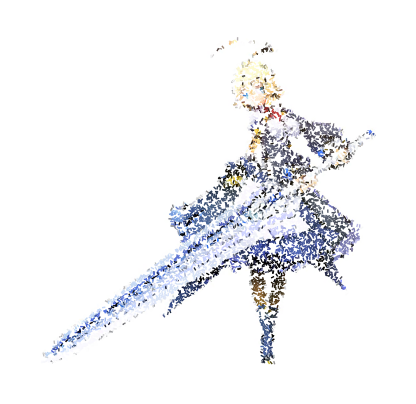

```mathematica
i=data[[1]];n=20000;s=10;
{x,y}=ImageDimensions[i]
pt=RandomChoice[Tuples@{Range[s,x-s],Range[s,y-s]},n];
Graphics[With[{col=RGBColor@ImageValue[i,Mean@@#]},{col,#}]&/@(Line/@Transpose[{pt,s{Sin[#],Cos[#]}&/@RandomReal[{0,2Pi},n]+pt}])]
```

```mathematica
LineWebPainting[-Graphics-,500]
```

-Graphics-

```mathematica
ColorCombine[LineWebPainting[#,200]&/@ColorSeparate[-Graphics-]]
```

-Graphics-